```mathematica
Integrate[x^4,x]
```

x^5/5

```mathematica
Integrate[x^(-2),x]
```

-1/x

```mathematica
Integrate[x^(5/4),x]
```

(4 x^(9/4))/9

```mathematica
Integrate[x^(-1/2),x]
```

2 √x

```mathematica
Integrate[x^(-1/3),x]
```

(3 x^(2/3))/2

```mathematica
Integrate[Exp[x],x]
```

ⅇ^x

```mathematica
Integrate[x^(-1),x]
```

Log[x]

```mathematica
Integrate[3x^2,x]
```

x^3

```mathematica
Integrate[4Exp[x],x]
```

4 ⅇ^x

```mathematica
Integrate[4Exp[4x],x]
```

ⅇ^(4 x)

```mathematica
Integrate[x^(-3)+x-1,x]
```

-1/(2 x^2)-x+x^2/2

```mathematica
Integrate[x^7-4x+2,x]
```

2 x-2 x^2+x^8/8

```mathematica
Integrate[x^(1/7)+x^{-1/7},x]
```

{(7 x^(6/7))/6+(7 x^(8/7))/8}

```mathematica
Integrate[Exp[a x],x]
```

ⅇ^(a x)/a

```mathematica
Integrate[Exp[4x],x]
```

ⅇ^(4 x)/4

```mathematica
Assuming[lambda>0,Integrate[Exp[-lambda x],{x,0,Infinity}]]
```

1/lambda

```mathematica
Assuming[lambda>0,Integrate[lambda Exp[-lambda x],{x,0,x}]]
```

1-ⅇ^(-lambda x)

```mathematica
Assuming[x>1,Integrate[1/x^2,{x,1,x}]]
```

(-1+x)/x

```mathematica
Assuming[x>1,Integrate[1/xx^2,{xx,1,x}]]
```

(-1+x)/x

```mathematica
Integrate[3-6x^2,{x,0,x}]
```

3 x-2 x^3

```mathematica
Integrate[8/7-2/7 x,{x,0,x}]
```

(8 x)/7-x^2/7

## Examples (g2)

```mathematica
Integrate[3/8*x^2-3/2*x+3/2,{x,0,2}]
```

1

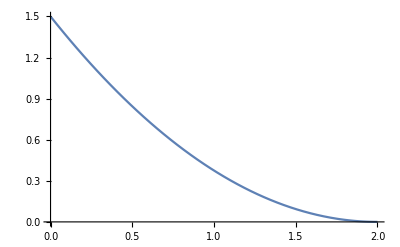

```mathematica
Plot[3/8*x^2-3/2*x+3/2,{x,0,2}]
```

```mathematica
F=Integrate[3/8*t^2-3/2*t+3/2,{t,0,x}]
```

(3 x)/2-(3 x^2)/4+x^3/8

Let’s check if the CDF has a value of 1 at the end point x=2.

```mathematica
F/.x->2
```

1

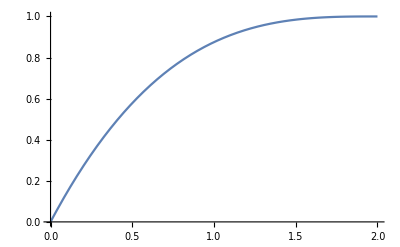

```mathematica
Plot[F,{x,0,2}]
```

## Now g1

4-x^2

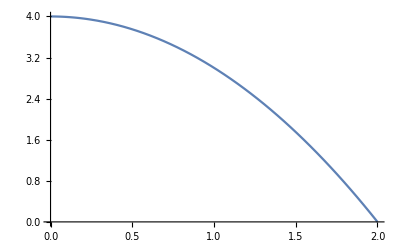

```mathematica
g1=4-x^2
Plot[g1,{x,0,2}]
```

```mathematica
A=Integrate[g1,{x,0,2}]
```

16/3

```mathematica
f1 = 1/A*g1
```

3/16 (4-x^2)

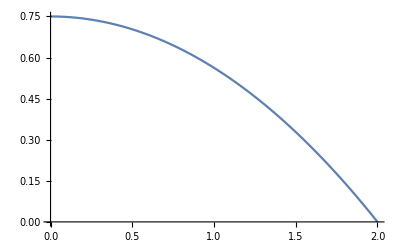

```mathematica
Plot[f1,{x,0,2}]
```

```mathematica
Integrate[f1,{x,0,2}]
```

1

We now have f1 is the pdf.  So to get the CDF we integrate the PDF from the left most bound (0) to x.

```mathematica
F1=Integrate[f1,{x,0,x}]
```

(3 x)/4-x^3/16

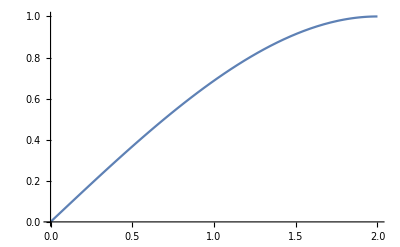

```mathematica
Plot[F1,{x,0,2}]
```

## Now g3

```mathematica
g3=1/x^2
```

1/x^2

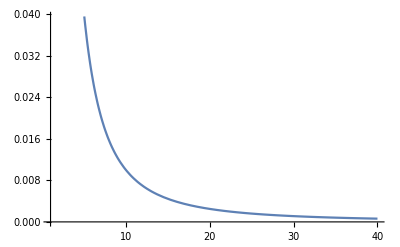

```mathematica
Plot[g3,{x,1,40}]
```

```mathematica
A=Integrate[g3,{x,1,Infinity}]
```

1

```mathematica
f3=1/A*g3
```

1/x^2

```mathematica
F=Assuming[x>1,Integrate[g3,{x,1,x}]]
```

(-1+x)/x

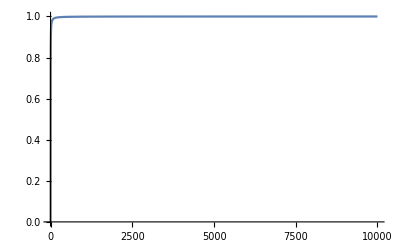

```mathematica
Plot[F,{x,1,10000},PlotRange->{0,1}]
```